## 1. domača naloga

#### Učni list - Naravna in cela števila

19. Jamarji se morajo na strmem kraškem pobočju pred spustom v globoko brezno od parkirišča povzpeti za 270 metrov. Koliko metrov pod izhodiščem je dno tega brezna, če je njegova globina 357 metrov?

```mathematica
357 - 270
```

87

Odgovor - Dno brezna je 87 metrov pod nivojem parkirišča.

#### Učni list - Deljivost

18.  Izračunaj največji skupni delitelj in najmanjši skupni večkratnik naslednjih števil:

```mathematica
GCD[72, 162, 252]  
LCM[72, 162, 252]
```

18

4536

```mathematica
GCD[84, 196, 308]
LCM[84, 196, 308]
```

28

6468

```mathematica
GCD[104, 156, 286]
LCM[104, 156, 286]
```

26

3432

```mathematica
GCD[252, 588, 896]
LCM[252, 588, 896]
```

28

56448

```mathematica
GCD[378, 630, 1575]
LCM[378, 630, 1575]
```

63

9450

```mathematica
GCD[414, 920, 4508]
LCM[414, 920, 4508]
```

46

405720

#### Učni list - Potence

8. Poenostavi:

```mathematica
Simplify[((4 x^4)^3) / (2x)^5]
```

2 x^7

```mathematica
Simplify[((18x^5y^(10))^3)/ (3x y^6)^5]
```

24 x^10

```mathematica
Simplify[(16x^5 y^(14))^3 /(2 x y^6)^7]
```

32 x^8

```mathematica
Simplify[(9x^6y^7)(x^2y)^7 /(3x^(16)y^(12))^2]
```

1/(x^12 y^10)

```mathematica
Simplify[(x^3y)^7 (8x^2y^5)^3 / (2x y^2)^8]
```

2 x^19 y^6

```mathematica
Simplify[(3x^2y^4z^3)^3 (81x^5 y^2 z^3)^7 / (27x^4 y^2 z^3)^(10)]
```

3 x y^6

#### Učni list - Računanje z izrazi

17. Kubiraj:

```mathematica
Expand[(x+4)^3]
```

64+48 x+12 x^2+x^3

```mathematica
Expand[(y-7)^3]
```

-343+147 y-21 y^2+y^3

```mathematica
Expand[(2z + 5)^3]
```

125+150 z+60 z^2+8 z^3

```mathematica
Expand[(6t-1)^3]
```

-1+18 t-108 t^2+216 t^3

#### Učni list - Realna števila

14. Reši enačbo:

```mathematica
Solve[Abs[x-6] == 8, x]
```

{{x→-2},{x→14}}

```mathematica
Solve[Abs[x+1] == 7, x]
```

{{x→-8},{x→6}}

```mathematica
Solve[Abs[3x-2]== 10, x]
```

{{x→-8/3},{x→4}}

```mathematica
Solve[Abs[5x+4] == 19, x]
```

{{x→-23/5},{x→3}}

```mathematica
Solve[Abs[2x+5] == Abs[4x-7],x]
```

{{x→1/3},{x→6}}

```mathematica
Solve[Abs[(1/4)x- (5/8)] == Abs[(-3/8)x +(1/2)], x]
```

{{x→-1},{x→9/5}}

#### Učni list - Linearna enačba

4. Reši enačbo

```mathematica
Solve[(2x-1)/3 == 3x + 5, x]
```

{{x→-16/7}}

```mathematica
Solve[(3x+5)/4 + 1 == (5x)/(12), x]
```

{{x→-27/4}}

```mathematica
Solve[(4x-3)/6 -(3/4) == x/9, x]
```

{{x→9/4}}

```mathematica
Solve[(2x-5)/7 - (4/3) == x/2, x]
```

{{x→-86/9}}

```mathematica
Solve[(4x-3)/7 == 2 - (x-5)/3, x]
```

{{x→86/19}}

```mathematica
Solve[(3x-5)/8 == 1- (x-2)/3, x]
```

{{x→55/17}}

#### Učni list - Sistemi linearnih enačb

30. Reši sistem treh linearnih enačb s tremi neznankami:

```mathematica
Solve[3x-2y-z==11 && 2x+5y-3z==-14 && 5x-y+2z==15, {x, y, z}]
```

{{x→2,y→-3,z→1}}

```mathematica
Solve[7x+y+z==-11 && 4x+y-3z==7 && -3x-4y+2z==-24, {x, y, z}]
```

{{x→-2,y→6,z→-3}}

```mathematica
Solve[2x+4y+z==19 && 5x-y-2z==8 && 3x+2y-3z==17, {x, y, z}]
```

{{x→2,y→4,z→-1}}

```mathematica
Solve[2(x-y)+z==4 && 3(x-z)+y==2 && 4(y-z)+x==-3, {x, y, z}]
```

{{x→1,y→-1,z→0}}

#### Učni list - Linearna funkcija

40. V koordinatnem sistemu nariši množico točk (x, y), za katero hkrati veljajo pogoji:

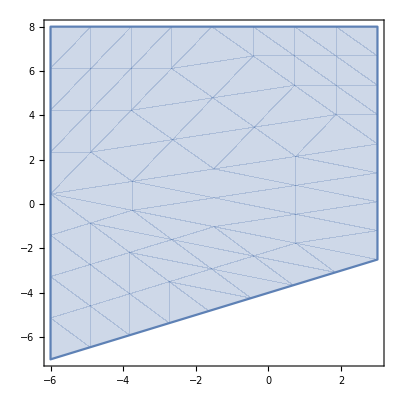

```mathematica
R = ImplicitRegion[y > (1/2)x -4 && x ≤ 3, {x, y}];
RegionPlot[R]
```

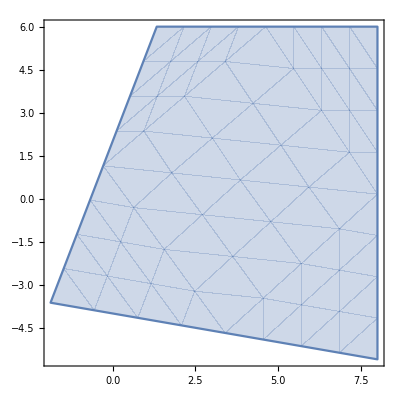

```mathematica
S = ImplicitRegion[y ≤ 3x + 2 && y > -(1/5)x - 4, {x, y}];
RegionPlot[S]
```

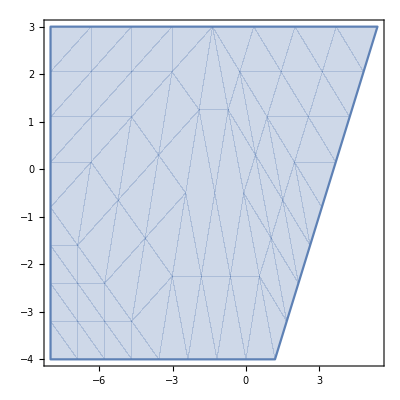

```mathematica
T = ImplicitRegion[-4 < y ≤ 3 && y ≥ (5/3)x - 6, {x, y}];
RegionPlot[T]
```

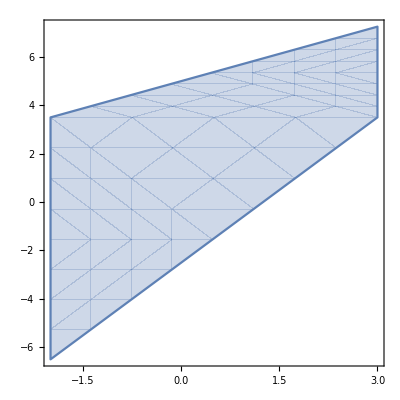

```mathematica
P = ImplicitRegion[-2 ≤ x < 3 && y ≥ 2x - (5/2) && y < (3/4)x + 5, {x, y}];
RegionPlot[P]
```

#### Učni list - Logaritem 1

3. Z uporabo definicije logaritma reši naslednje logaritemske enačbe:

```mathematica
Solve[Log[3, x] == 2]
```

{{x→9}}

```mathematica
Solve[Log[10, x] == -2]
```

{{x→1/100}}

```mathematica
Solve[Log[9, x] == 3/2]
```

{{x→27}}

```mathematica
Solve[Log[9, x] == -(3/2)]
```

{{x→1/27}}

```mathematica
Solve[Log[125, x] == 1/3]
```

{{x→5}}

```mathematica
Solve[Log[1/5, x] == -3]
```

{{x→125}}

#### Učni list - Polinomi 2

16. Izračunaj ničle in nariši graf polinoma:

{{x→-1},{x→-1},{x→3}}

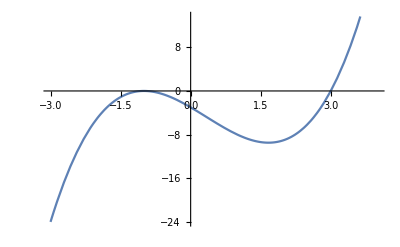

```mathematica
p[x_] = x^3 - x^2 - 5x - 3;
Solve[p[x] == 0]
Plot[p[x], {x, -3, 4}]
```

{{x→-1},{x→3},{x→3}}

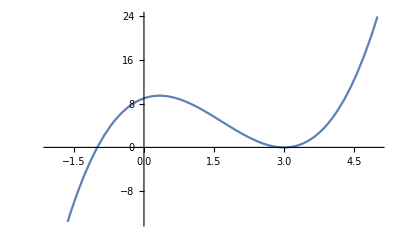

```mathematica
q[x_] = x^3 - 5x^2 + 3x + 9;
Solve[q[x] == 0]
Plot[q[x], {x, -2, 5}]
```

{{x→-3},{x→-1},{x→-1}}

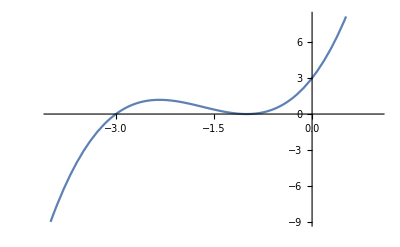

```mathematica
r[x_] = x^3 + 5x^2 + 7x + 3;
Solve[r[x] == 0]
Plot[r[x], {x, -4, 1}]
```

{{x→1},{x→4},{x→4}}

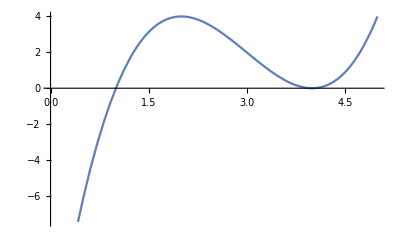

```mathematica
s[x_] = x^3 - 9x^2 + 24x - 16;
Solve[s[x] == 0]
Plot[s[x], {x, 0, 5}]
```